```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## Physics 449 - Li Project Lauren Laufman Lucky Volety Doreen Beeler

### Introduction

The goal of this project is to use your knowledge of quantum mechanics to compute many of the low-lying energy levels of the Li atom. Since the Li atom has 3 electrons, you will learn how to construct 3-electron wavefunctions that satisfy the Pauli exclusion principle. You will use both variational methods and a basis set expansion to get your final results. You will learn about Slater determinants and exchange operators. You will compare your calculations to experiment, and you should be able to attain accuracies for most of the properties of Li to better than 1% error, and some to less that 0.1% error. Quantum mechanics really works!

To get started, you will first solve the simpler problem of the 2-electron Li^(++) ion. This simpler calculation is very similar to that of the He atom, written up by a 449 alumnus (Robert Massé) in the paper “Accurate energies of the He atom with undergraduate quantum mechanics”, Am. J. Phys. 83, 730 (2015), which you will need to read carefully. To the methods there, you will add a variational calculation for the ground state, then use a basis set founded on that variational calculation to both improve the ground state energy a bit, and to get the energies of some of the low-lying excited states.

The addition of the third electron in the neutral Li atom adds some complexity to the problem. For Li^+ it is sufficient to use an non-symmetrized basis set; the exchange symmetry of the Hamiltonian gives spatial eigenfunctions that are either symmetric or anti-symmetric on interchange, and these are easily identified. For the 3-electron problem, one cannot be so casual and explicitly anti-symmetrized wavefunctions are necessary. To this end, you will construct Slater determinants that satisfy this requirement, and use your knowledge of commutation relations to simplify the calculation of matrix elements of the Hamiltonian. You will again first perform a variational calculation of the ground state energy, then use a related basis set expansion to get the excited states. You will then use a quantum defect analysis of your results to deduce the ionization energy of Li, to an accuracy better than 0.1%.

You will do the above calculations in small 2 or 3 person teams. To ensure proper progress, there will be intermediate due dates for various parts of the project. Once you complete your calculations, each student will write a short (3-5 journal pages) paper on your work. There will be a prize for the best paper and there is also the potential to submit the paper, suitably revised, for publication in a refereed journal.

### Li^(++)

The Hamiltonian for the single-electron Li^(++) atom is just like hydrogen, but with a charge
of 3 on the nucleus. In atomic units
(Ĥ)^(++)=-1/2∇^2 -Z/r
with Z=3 for the Li nucleus.

1) Show that the radial eigenfunctions of (Ĥ)^(++) are (P̂)_(n l)^(++)(r)=N(Z) P_(n,l)(Z r), where P_(n,l)(r) are the eigenfunctions of hydrogen. Find the normalization factor N(Z). Find the energies.

[-ℏ^2/(2 m)∇_r^2 +(l(l+1)ℏ^2)/(2 m r^2)-(Z e^2)/r]P_(n l)=E P_(n l)
scale: r=a_z s
[-ℏ^2/(2 m a_z^2)∇_s^2 +(l(l+1)ℏ^2)/(2 m a_z^2 s^2)-(Z e^2)/(a_z s)]P_(n l)=E P_(n l)
(m a_z^2)/ℏ^2 [-ℏ^2/(2 m a_z^2)∇_s^2 +(l(l+1)ℏ^2)/(2 m a_z^2 s^2)-(Z e^2)/(a_z s)]P_(n l)=(m a_z^2)/ℏ^2 E P_(n l)
[-1/2∇_s^2 +(l(l+1))/(2 s^2)-(m a_z Z e^2)/ℏ^2 1/s]P_(n l)=E_s P_(n l)

E_s=(m a_z^2)/ℏ^2 E
(m a_z Z e^2)/ℏ^2=1 ⇒a_z=1/Z ℏ^2/(m e^2)=a_0/Z
r=a_z s=(a_0 s)/Z
E_s=ℏ^2/(m Z^2 e^4)E
We go from previous homeworks with Z=1 and s=r/a_0 to s=(r Z)/a_0. Thus before our solution was just the P_(n l) now it’s modified, and P_(n l)^(++)(r)=N_z P_(n l)(Z r). To find the normalization factor:

```mathematica
$Assumptions=Z≥0&&Z∈Reals&&N∈Reals&&N≥0;
```

```mathematica
Solve[1==(∫_0^∞ (N Subscript[P, 7,2][Z s])(N Subscript[P, 7,2][Z s])ⅆs)^2,N]
```

{{N→-√Z},{N→-ⅈ √Z},{N→ⅈ √Z},{N→√Z}}

```mathematica
Subscript[P, n_,l_,z_][r_]:=√z Subscript[P, n,l][z r]
```

N=√Z
P_(n l)^(++)(r)=√Z P_(n l)(Z r)

Then we have that E_n=-(m Z^2 e^4)/(2 ℏ^2 n^2) so we just apply our scaling and get a new E_n=-Z^2/(2 n^2)
Also note that a_0=1 in our atomic units.
Test to check I did this right by plugging into Schrodinger equation:

```mathematica
Table[-1/2 D[(√3 Subscript[P, n,0][3 r]), r,r]-3/r (√3 Subscript[P, n,0][3 r])==(-9/(2 n^2))(√3 Subscript[P, n,0][3 r])//Simplify,{n,1,5}]
```

{True,True,True,True,True}

The energies for the first several n’s:

```mathematica
Table[-3^2/(2 n^2),{n,1,5}]//Simplify//N
```

{-4.5,-1.125,-0.5,-0.28125,-0.18}

### Li^+

The Hamiltonian for the two-electron Li^+ ion is (with Z=3) 
(Ĥ)^+=(Ĥ)^(++)(1)+(Ĥ)^(++)(2)+1/r_12=(Ĥ)_0+V_12=(-1/2(∇_1)^2-Z/r_1)+(-1/2(∇_2)^2-Z/r_2)+1/r_12
We are going to restrict our considerations to states of total angular momentum L=0, which we
assume is made of only of s-type single-electron orbitals P_(n 0)^(++)(r)=P_n^z(r)=N(z)P_(n,0)^(++)(z r). Here z≠Z is a parameter we will use for a variation calculation below. The basis states we will denote simply as n_1;n_2, whose representation in position space is r_1;r_2n_1;n_2≡P_(n_1 n_2)^+(r_1,r_2)=P_n_1^z(r_1)P_n_2^z(r_2).

2) Show that the matrix elements of (Ĥ)^+ are n_1;n_2(Ĥ)^+n_3;n_4=n_1(Ĥ)^(++)(1)n_3 δ_(n_2,n_4)+n_2(Ĥ)^(++)(2)n_4 δ_(n_1,n_3)+n_1;n_2 V_12 n_3;n_4
Write Mathematica routines to calculate (analytically) n_1(Ĥ)^(++)n_3 and n_1;n_2 V_12 n_3;n_4; check your results against the Massé paper for He.

(Ĥ)^+=(Ĥ)^(++)(1)+(Ĥ)^(++)(2)+1/r_12=(Ĥ)_0+V_12=(-1/2(∇_1)^2-Z/r_1)+(-1/2(∇_2)^2-Z/r_2)+1/r_12
r_1;r_2n_1;n_2≡P_(n_1 n_2)^+(r_1,r_2)=P_n_1^z(r_1)P_n_2^z(r_2)

n_1;n_2(Ĥ)^+n_3;n_4
=∫𝕕^3 r_1 𝕕^3 r_2 n_1;n_2r_1;r_2(Ĥ)^+r_1;r_2n_3;n_4
=∫𝕕^3 r_1 𝕕^3 r_2 ψ_n_1(r_1)ψ_n_2(r_2)(Ĥ)^+ψ_n_3(r_1)ψ_n_4(r_2)
=∫𝕕r_1 𝕕r_2 P_n_1^z(r_1)P_n_2^z(r_2)(Ĥ)^+P_n_3^z(r_1)P_n_4^z(r_2)
=∫𝕕r_1 𝕕r_2 P_n_1^z(r_1)P_n_2^z(r_2)((Ĥ)^(++)(1)+(Ĥ)^(++)(2)+V_12)P_n_3^z(r_1)P_n_4^z(r_2)
=∫𝕕r_1 𝕕r_2 P_n_2^z(r_2)P_n_4^z(r_2) P_n_1^z(r_1)(Ĥ)^(++)(1)P_n_3^z(r_1)+∫𝕕r_1 𝕕r_2 P_n_1^z(r_1)P_n_3^z(r_1)P_n_2^z(r_2)(Ĥ)^(++)(2)P_n_4^z(r_2)+∫𝕕r_1 𝕕r_2 P_n_1^z(r_1)P_n_2^z(r_2)V_12 P_n_3^z(r_1)P_n_4^z(r_2)
=n_1(Ĥ)^(++)(1)n_3 δ_(n_2,n_4)+n_2(Ĥ)^(++)(2)n_4 δ_(n_1,n_3)+n_1;n_2 V_12 n_3;n_4
note that the delta’s come from the orthogonality of the P’s

n_1(Ĥ)^(++)n_3=

```mathematica
Subscript[nHn, n1_,n3_,z_,Z_]:=∫_0^∞ Subscript[P, n1,0,z][r](-1/2 D[Subscript[P, n3,0,z][r], r,r]-Z/r Subscript[P, n3,0,z][r])ⅆr
```

n_1;n_2 V_12 n_3;n_4=

```mathematica
Subscript[V12, n1_,n2_,n3_,n4_,z_]:=∫_0^∞ ∫_0^∞ Subscript[P, n1,0,z][r1]Subscript[P, n2,0,z][r2]Min[1/r2,1/r1]Subscript[P, n3,0,z][r1]Subscript[P, n4,0,z][r2]ⅆr2ⅆr1
```

alternatively, numerical integration is faster:

```mathematica
Subscript[V12, {n1_,n2_},{n3_,n4_},z_]:=NIntegrate[Subscript[P, n1,0,z][r1]Subscript[P, n2,0,z][r2]Min[1/r2,1/r1]Subscript[P, n3,0,z][r1]Subscript[P, n4,0,z][r2],{r2,0,∞},{r1,0,∞},AccuracyGoal->7]
```

Now, to test for Helium to make sure it matches the paper

```mathematica
st=DeleteDuplicates[Table[{{1,i},{i,1}},{i,4}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1}}

```mathematica
Subscript[n1Hn3, {n1_,n2_},{n3_,n4_},z_,Z_]:=n2,n4 NIntegrate[Subscript[P, n1,0,z][r] (-1/2 D[Subscript[P, n3,0,z][r], r,r]-Z/r Subscript[P, n3,0,z][r]),{r,0,∞}]//Simplify
```

```mathematica
Subscript[n2Hn4, {n1_,n2_},{n3_,n4_},z_,Z_]:=n1,n3 NIntegrate[Subscript[P, n2,0,z][r] (-1/2 D[Subscript[P, n4,0,z][r], r,r]-Z/r Subscript[P, n4,0,z][r]),{r,0,∞}]//Simplify
```

this here is the V matrix

```mathematica
Vmat=Table[Subscript[V12, st⟦i⟧,st⟦j⟧,2],{i,Length[st]},{j,Length[st]}]//N;Vmat//MF
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

(1.25 | -0.179 | -0.179 | 0.0879 | 0.0879 | -0.0552 | -0.0552
-0.179 | 0.42 | 0.0439 | -0.101 | -0.0224 | 0.0574 | 0.0143
-0.179 | 0.0439 | 0.42 | -0.0224 | -0.101 | 0.0143 | 0.0574
0.0879 | -0.101 | -0.0224 | 0.199 | 0.0115 | -0.0577 | -0.00735
0.0879 | -0.0224 | -0.101 | 0.0115 | 0.199 | -0.00734 | -0.0577
-0.0552 | 0.0574 | 0.0143 | -0.0577 | -0.00734 | 0.115 | 0.00468
-0.0552 | 0.0143 | 0.0574 | -0.00735 | -0.0577 | 0.00468 | 0.115)

```mathematica
H1=DiagonalMatrix[Table[Subscript[n1Hn3, st⟦i⟧,st⟦i⟧,2,2],{i,Length[st]}]];
```

```mathematica
H2=DiagonalMatrix[Table[Subscript[n2Hn4, st⟦i⟧,st⟦i⟧,2,2],{i,Length[st]}]];
```

```mathematica
H0=H1+H2;H0//MF
```

(-4. | 0 | 0 | 0 | 0 | 0 | 0
0 | -2.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2.22 | 0 | 0 | 0
0 | 0 | 0 | 0 | -2.22 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2.12 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2.12)

```mathematica
H=H1+H2+Vmat;H//MF
```

(-2.75 | -0.179 | -0.179 | 0.0879 | 0.0879 | -0.0552 | -0.0552
-0.179 | -2.08 | 0.0439 | -0.101 | -0.0224 | 0.0574 | 0.0143
-0.179 | 0.0439 | -2.08 | -0.0224 | -0.101 | 0.0143 | 0.0574
0.0879 | -0.101 | -0.0224 | -2.02 | 0.0115 | -0.0577 | -0.00735
0.0879 | -0.0224 | -0.101 | 0.0115 | -2.02 | -0.00734 | -0.0577
-0.0552 | 0.0574 | 0.0143 | -0.0577 | -0.00734 | -2.01 | 0.00468
-0.0552 | 0.0143 | 0.0574 | -0.00735 | -0.0577 | 0.00468 | -2.01)

This matches the matrix given in the He1s2s.nb handout! Interestingly, the paper’s H is missing a few negative signs as compared to the Mathematica file’s H, and I’m inclined to believe the latter is correct.

You are now ready to do a simple variational calculation of the ground state energy of Li^+. For your variational wavefunction, pick P_n_1^z(r_1)P_n_2^z(r_2), keeping z to be your variational parameter.

3) Minimize the ground-state (1 s^2) energy with respect to z, and compare your results to the NIST experimental energy. Make a physical argument why z<Z.

```mathematica
$Assumptions=z>0;
```

```mathematica
expectH=With[{n1=1,n2=1,n3=1,n4=1},Subscript[nHn, n1,n3,z,Z]+Subscript[nHn, n2,n4,z,Z]+Subscript[V12, n1,n2,n3,n4,z]]
```

(5 z)/8+z (z-2 Z)

```mathematica
normalize=With[{n1=1,n2=1,n3=1,n4=1},∫_0^∞ ∫_0^∞ Subscript[P, n1,0,z][r1]Subscript[P, n2,0,z][r2]Subscript[P, n3,0,z][r1]Subscript[P, n4,0,z][r2]ⅆr1ⅆr2]
```

1

```mathematica
ClearAll[ϵ]
```

```mathematica
ϵ[z_]=expectH/normalize
```

(5 z)/8+z (z-2 Z)

For the helium related stuff, to compare to Masse paper:

```mathematica
Tr[Solve[D[ϵ[z], z]==0,z]]/.Z->2
```

z→27/16

```mathematica
ϵ[27/16]/.Z->2
```

-729/256

For Li^+:

```mathematica
Minimize[ϵ[z],z]/.Z->3
```

{-1849/256,{z→43/16}}

```mathematica
%//N
```

{-7.22266,{z→2.6875}}

```mathematica
eval=(Minimize[ϵ[z],z]/.Z->3)⟦1⟧;
```

We know Z is the charge of the nucleus and z is the effective charge the electrons see. For Li^+, z is less than Z because adding electrons brings the total charge of the atom closer to zero, and also electrons repel each other. They’re then shielded a bit from the nucleus.

https://physics.nist.gov/PhysRefData/ASD/levels_form.html
Li^+ ionization = 5.55944459 Ry
Li^(++) ionization = 9.000229392 Ry

```mathematica
expt=-(5.55944459+9.000229392)/2
```

-7.27984

```mathematica
Print["% error = ",100(1-eval/expt)]
```

% error = 0.785467

Now make a somewhat more sophisticated calculation. Your variational wavefunction for the 1 s^2 state should be a pretty good representation. So use the set of functions P_n_1^z(r_1)P_n_2^z(r_2) as a basis, with z chosen as the result of your variational calculation. Make a list of the 17 lowest energy states and use those as a basis. Even though all the 17^2 integrals can be done analytically, in the interest of time it is useful to do them numerically.

4) Use your 17 state basis to construct the Hamiltonian for Li^+, and find the energy eigenvalues. How much better is your 1 s^2 energy?

this is a 17 by 17 matrix, calculated the same way we got the elements for #3, so through 1s9s and since 1s1s is it’s own thing it’s the odd number

```mathematica
st=DeleteDuplicates[Table[{{1,i},{i,1}},{i,9}]~Flatten~1]
```

{{1,1},{1,2},{2,1},{1,3},{3,1},{1,4},{4,1},{1,5},{5,1},{1,6},{6,1},{1,7},{7,1},{1,8},{8,1},{1,9},{9,1}}

```mathematica
H1=Table[Subscript[n1Hn3, st⟦i⟧,st⟦j⟧,(43/16),3],{i,Length[st]},{j,Length[st]}];
```

```mathematica
H2=Table[Subscript[n2Hn4, st⟦i⟧,st⟦j⟧,(43/16),3],{i,Length[st]},{j,Length[st]}];
```

```mathematica
H0=H1+H2;
```

```mathematica
Vmat=Table[Subscript[V12, st⟦i⟧,st⟦j⟧,(43/16)],{i,Length[st]},{j,Length[st]}]//N;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
H=H1+H2+Vmat;
```

```mathematica
H//MF
```

(-7.22 | -0.0642 | -0.0642 | 0.0272 | 0.0272 | -0.0161 | -0.0161 | 0.0111 | 0.0111 | -0.00822 | -0.00822 | 0.00643 | 0.00643 | -0.00521 | -0.00521 | 0.00434 | 0.00434
-0.0642 | -5. | 0.059 | -0.0752 | -0.0302 | 0.0413 | 0.0192 | -0.0276 | -0.0136 | 0.0203 | 0.0103 | -0.0157 | -0.00813 | 0.0127 | 0.00664 | -0.0106 | -0.00556
-0.0642 | 0.059 | -5. | -0.0302 | -0.0752 | 0.0192 | 0.0413 | -0.0136 | -0.0276 | 0.0103 | 0.0203 | -0.00813 | -0.0157 | 0.00664 | 0.0127 | -0.00556 | -0.0106
0.0272 | -0.0752 | -0.0302 | -4.68 | 0.0155 | -0.047 | -0.00987 | 0.0283 | 0.007 | -0.0199 | -0.0053 | 0.0151 | 0.00419 | -0.012 | -0.00342 | 0.00992 | 0.00287
0.0272 | -0.0302 | -0.0752 | 0.0155 | -4.68 | -0.00987 | -0.047 | 0.007 | 0.0283 | -0.0053 | -0.0199 | 0.00419 | 0.0151 | -0.00342 | -0.012 | 0.00287 | 0.00992
-0.0161 | 0.0413 | 0.0192 | -0.047 | -0.00987 | -4.57 | 0.00629 | -0.0311 | -0.00446 | 0.0198 | 0.00338 | -0.0144 | -0.00267 | 0.0112 | 0.00218 | -0.00911 | -0.00183
-0.0161 | 0.0192 | 0.0413 | -0.00987 | -0.047 | 0.00629 | -4.57 | -0.00446 | -0.0311 | 0.00338 | 0.0198 | -0.00267 | -0.0144 | 0.00218 | 0.0112 | -0.00183 | -0.00911
0.0111 | -0.0276 | -0.0136 | 0.0283 | 0.007 | -0.0311 | -0.00446 | -4.53 | 0.00316 | -0.0219 | -0.00239 | 0.0145 | 0.00189 | -0.0108 | -0.00155 | 0.00858 | 0.0013
0.0111 | -0.0136 | -0.0276 | 0.007 | 0.0283 | -0.00446 | -0.0311 | 0.00316 | -4.53 | -0.00239 | -0.0219 | 0.00189 | 0.0145 | -0.00155 | -0.0108 | 0.0013 | 0.00858
-0.00822 | 0.0203 | 0.0103 | -0.0199 | -0.0053 | 0.0198 | 0.00338 | -0.0219 | -0.00239 | -4.5 | 0.00181 | -0.0163 | -0.00143 | 0.011 | 0.00117 | -0.00838 | -0.000981
-0.00822 | 0.0103 | 0.0203 | -0.0053 | -0.0199 | 0.00338 | 0.0198 | -0.00239 | -0.0219 | 0.00181 | -4.5 | -0.00143 | -0.0163 | 0.00117 | 0.011 | -0.000981 | -0.00838
0.00643 | -0.0157 | -0.00813 | 0.0151 | 0.00419 | -0.0144 | -0.00267 | 0.0145 | 0.00189 | -0.0163 | -0.00143 | -4.49 | 0.00114 | -0.0125 | -0.000927 | 0.00864 | 0.000776
0.00643 | -0.00813 | -0.0157 | 0.00419 | 0.0151 | -0.00267 | -0.0144 | 0.00189 | 0.0145 | -0.00143 | -0.0163 | 0.00114 | -4.49 | -0.000927 | -0.0125 | 0.000776 | 0.00864
-0.00521 | 0.0127 | 0.00664 | -0.012 | -0.00342 | 0.0112 | 0.00218 | -0.0108 | -0.00155 | 0.011 | 0.00117 | -0.0125 | -0.000927 | -4.48 | 0.000758 | -0.00992 | -0.000634
-0.00521 | 0.00664 | 0.0127 | -0.00342 | -0.012 | 0.00218 | 0.0112 | -0.00155 | -0.0108 | 0.00117 | 0.011 | -0.000927 | -0.0125 | 0.000758 | -4.48 | -0.000634 | -0.00992
0.00434 | -0.0106 | -0.00556 | 0.00992 | 0.00287 | -0.00911 | -0.00183 | 0.00858 | 0.0013 | -0.00838 | -0.000981 | 0.00864 | 0.000776 | -0.00992 | -0.000634 | -4.47 | 0.000531
0.00434 | -0.00556 | -0.0106 | 0.00287 | 0.00992 | -0.00183 | -0.00911 | 0.0013 | 0.00858 | -0.000981 | -0.00838 | 0.000776 | 0.00864 | -0.000634 | -0.00992 | 0.000531 | -4.47)

```mathematica
eval=Eigenvalues[H]
```

{-7.22701,-5.06543,-4.9809,-4.70306,-4.6788,-4.5876,-4.57727,-4.53655,-4.53127,-4.50961,-4.50661,-4.49371,-4.49188,-4.4835,-4.48203,-4.43792,-4.38792}

For the 1 s^2 energy:

```mathematica
expt=-(5.55944459+9.000229392)/2
```

-7.27984

```mathematica
Print["% error = ",100(1-eval⟦1⟧/expt)]
```

% error = 0.725628

This is better than before, a smaller % error.

5) Looking at your eigenvectors, which ones are singlets and which ones are triplets? Calculate the 1s2s singlet and triplet energies, and compare to experiment. Also compare the singlet-triplet splitting to experiment.

```mathematica
{eval,evec}=Eigensystem[H];
```

```mathematica
evec//MF
```

(0.999 | 0.0273 | 0.0273 | -0.00927 | -0.00927 | 0.00515 | 0.00515 | -0.00344 | -0.00344 | 0.00252 | 0.00252 | -0.00196 | -0.00196 | 0.00158 | 0.00158 | -0.00132 | -0.00132
1.2×10^-9 | 0.702 | -0.702 | 0.0812 | -0.0812 | -0.0245 | 0.0245 | 0.0133 | -0.0133 | -0.0089 | 0.0089 | 0.00657 | -0.00657 | -0.00516 | 0.00516 | 0.00423 | -0.00423
-0.0317 | 0.671 | 0.671 | 0.205 | 0.205 | -0.065 | -0.065 | 0.0377 | 0.0377 | -0.0261 | -0.0261 | 0.0198 | 0.0198 | -0.0158 | -0.0158 | 0.0131 | 0.0131
-7.61×10^-8 | -0.0691 | 0.0691 | 0.672 | -0.672 | 0.197 | -0.197 | -0.0522 | 0.0522 | 0.029 | -0.029 | -0.0198 | 0.0198 | 0.015 | -0.015 | -0.0121 | 0.0121
-0.0142 | 0.14 | 0.14 | -0.596 | -0.596 | -0.338 | -0.338 | 0.0825 | 0.0825 | -0.0479 | -0.0479 | 0.0337 | 0.0337 | -0.0261 | -0.0261 | 0.0214 | 0.0214
-3.91×10^-9 | -0.0308 | 0.0308 | 0.147 | -0.147 | -0.61 | 0.61 | -0.315 | 0.315 | 0.065 | -0.065 | -0.0371 | 0.0371 | 0.0261 | -0.0261 | -0.0205 | 0.0205
0.00861 | -0.0728 | -0.0728 | 0.186 | 0.186 | -0.491 | -0.491 | -0.457 | -0.457 | 0.0758 | 0.0758 | -0.0475 | -0.0475 | 0.0349 | 0.0349 | -0.0282 | -0.0282
-2.87×10^-9 | -0.0189 | 0.0189 | 0.0744 | -0.0744 | -0.197 | 0.197 | 0.517 | -0.517 | 0.427 | -0.427 | -0.0601 | 0.0601 | 0.0389 | -0.0389 | -0.0295 | 0.0295
-0.00592 | 0.0472 | 0.0472 | -0.104 | -0.104 | 0.201 | 0.201 | -0.368 | -0.368 | -0.554 | -0.554 | 0.0461 | 0.0461 | -0.0403 | -0.0403 | 0.033 | 0.033
-6.54×10^-9 | 0.0132 | -0.0132 | -0.0479 | 0.0479 | 0.109 | -0.109 | -0.218 | 0.218 | 0.402 | -0.402 | 0.523 | -0.523 | -0.0366 | 0.0366 | 0.0373 | -0.0373
-0.00437 | 0.0337 | 0.0337 | -0.0693 | -0.0693 | 0.12 | 0.12 | -0.189 | -0.189 | 0.239 | 0.239 | 0.621 | 0.621 | 0.00287 | 0.00287 | 0.0316 | 0.0316
3.79×10^-9 | 0.00986 | -0.00986 | -0.0343 | 0.0343 | 0.0722 | -0.0722 | -0.13 | 0.13 | 0.212 | -0.212 | -0.277 | 0.277 | -0.596 | 0.596 | -0.00135 | 0.00135
0.00339 | -0.0257 | -0.0257 | 0.0509 | 0.0509 | -0.0834 | -0.0834 | 0.123 | 0.123 | -0.158 | -0.158 | 0.115 | 0.115 | 0.658 | 0.658 | 0.0643 | 0.0643
4.96×10^-8 | -0.00819 | 0.00819 | 0.0278 | -0.0278 | -0.0562 | 0.0562 | 0.0954 | -0.0954 | -0.146 | 0.146 | 0.199 | -0.199 | -0.173 | 0.173 | -0.629 | 0.629
0.00319 | -0.024 | -0.024 | 0.0465 | 0.0465 | -0.0738 | -0.0738 | 0.105 | 0.105 | -0.134 | -0.134 | 0.138 | 0.138 | -0.0246 | -0.0246 | -0.666 | -0.666
-1.08×10^-8 | -0.0334 | 0.0334 | 0.101 | -0.101 | -0.173 | 0.173 | 0.239 | -0.239 | -0.291 | 0.291 | 0.323 | -0.323 | -0.334 | 0.334 | 0.318 | -0.318
-0.0204 | 0.139 | 0.139 | -0.219 | -0.219 | 0.271 | 0.271 | -0.293 | -0.293 | 0.292 | 0.292 | -0.276 | -0.276 | 0.251 | 0.251 | -0.221 | -0.221)

“Note that the eigenstates are exchange symmetric, or antisymmetric!   The antisymmetric ones have zero 1s1s coefficient.”
This probably means the first column is the 1s1s coefficient.

The lowest three eigenvalues [of H] correspond to the ground state and the 1s2s triplet and singlet states.

Use Li II on the database, where the limit line says 1 s^2 S_(1/2). on this page, go up to the top, and the first three are their ground, 1s2s triplet, and singlet. need to adjust base level from zero, which is the experiment above value for ground

In order ground, triplet, singlet, experimental values from database in Hartrees:

```mathematica
expt=1/2(-5.55944459-9.000229392+{0,4.3379499,4.477735})
```

{-7.27984,-5.11086,-5.04097}

Our values obtained by thad’s method:

```mathematica
eval⟦;;3⟧
```

{-7.22701,-5.06543,-4.9809}

Error calculation:

```mathematica
Print["% error = ",100(1-eval⟦;;3⟧/expt)]
```

% error = {0.725628,0.888895,1.1917}

Singlet-triplet splitting probably means the difference in energy between the 1s2s singlet and 1s2s triplet:

```mathematica
eval⟦3⟧-eval⟦2⟧
```

0.0845355

```mathematica
Print["% error = ",100Abs[(1-(eval⟦3⟧-eval⟦2⟧)/(expt⟦3⟧-expt⟦2⟧))]]
```

% error = 20.9506

### Li

6) Calculate [(P̂)_23,(P̂)_13]. Give your answer in terms of ℒ̂ and ℛ̂. Show that [ℒ̂,Ĥ]=[ℛ̂,Ĥ]=0. Show that (ℒ̂)^3=1 and (ℒ̂)^†=ℛ̂. Are (ℒ̂)^† and ℛ̂ unitary, Hermitian, or what?

[P_23,P_13]a;b;c=P_23 P_13 a;b;c-P_13 P_23 a;b;c=P_23 c;b;a-P_13 a;c;b
=c;a;b-b;c;a
=ℛ̂ a;b;c-ℒ̂ a;b;c=(ℛ̂-ℒ̂)a;b;c

[ℒ̂,Ĥ]=[P_13 P_23,Ĥ]=[P_13,Ĥ]P_23+P_13[P_23,Ĥ]=0 because commutation relations and [P_ij,Ĥ]=0

[ℛ̂,Ĥ]=[P_23 P_13,Ĥ]=[P_23,Ĥ]P_13+P_23[P_13,Ĥ]=0 because commutation relations and [P_ij,Ĥ]=0

(ℒ̂)^3 a;b;c=(P_13 P_23)^3 a;b;c=(P_13 P_23)^2 b;c;a=(P_13 P_23)c;a;b=1a;b;c

If an operator is Hermitian, it’s equal to its dagger. 

first: ℒ
a b cℒA B C=a b cB C A=aBbCcA
then: ℒ^†
A B Cℒa b c=A B Cb c a=AbBcCa
As you can see from the first having ⟨c|A⟩ and the second having ⟨A|b⟩, these two are not equal. Thus ℒ≠ℒ^† and is not Hermitian.

Now for ℛ
a b cℛA B C=a b cC A B=aCbAcB
and ℛ^†
A B Cℛa b c=A B Cc a b=AcBaCb
Again, they are not equal. ℛ≠ℛ^† and thus is not Hermitian.

However, from this you can see that ℒ^†=ℛ and that ℒ=ℛ^†.

An operator U that satisfies U^†U=𝟙 is called unitary.

ℒ^†ℒ=ℛ ℒ=P_23 P_13 P_13 P_23=P_23 P_13^2 P_23=P_23 1 P_23=P_23^2=1
ℒ^†ℒa b c=ℛ ℒa b c=P_23 P_13 P_13 P_23 a b c=P_23 P_13 b c a=a b c
ℒ is unitary. ℒ doesn’t equal ℒ^† so it’s not Hermitian.
ℛ^†=ℒ thus obviously ℛ is also unitary and not Hermitian.

Additionally, we can find if the P_ij are Hermitian or not, which will help with finding 𝒜^† later on. 
a b c P_12 A B C=a b cB A C=aBbAcC
A B C P_12 a b c=A B Cb a c=AbBaCc
These are equal. Thus P_ij^†=P_ij and P_ij is Hermitian. Additionally, it’s unitary since P_ij^†P_ij=P_ij P_ij=P_ij^2=1

7) Prove that if ψ is an eigenvector of (P̂)_12 and (P̂)_23 with an eigenvalue -1, it is also an eigenvector of (P̂)_13with eigenvalue -1. One way to do this is to calculate Q̂=(P̂)_23(P̂)_12. Show that Q̂ ψ=ψ. Then (P̂)_13 ψ=(P̂)_13 Q̂ ψ=...

Let Q=P_23 P_12
Qψ=P_23_P12 ψ=P_23(-ψ)=-(-ψ)=ψ
P_13 ψ=P_13 Qψ=P_13 P_23 P_12 ψ=(P_13 P_23)P_12 ψ=(P_23 P_12)P_12 ψ=P_23 P_12^2 ψ=P_23 ψ=-ψ
P_13 ψ=-ψ

### Slater Determinants and the Pauli Exclusion Principle

8) Show that a Slater determinant for Li can be written as  ∥ad,bu,cu∥=1/(√6)(1+ℒ+ℛ)(1-P_23)ad,bu,cu=1/(√6)𝒜ad,bu,cu. We might call the operator 𝒜 an “antisymmetrizer” as it converts a product state into a Slater determinant.

∥a d,b u,c u∥=det|φ[a] d(1) | φ[b] u(1) | φ[c] u(1)
φ[a] d(2) | φ[b] u(2) | φ[c] u(2)
φ[a] d(3) | φ[b] u(3) | φ[c] u(3)|
=1/(√6)(a d,b u,c u-ad,cu,bu-bu,ad,cu+bu,cu,ad+cu,ad,bu-cu,bu,ad)

1/(√6)(1+ℒ+ℛ)(1-P_23)=1/(√6)(1+ℒ+ℛ-P_23-ℒ P_23-ℛ P_23)
=1/(√6)(1+P_13 P_23+P_23 P_13-P_23-P_13 P_23 P_23-P_23 P_13 P_23)
=1/(√6)(1+P_13 P_23+P_23 P_13-P_23-P_13-P_12)

1/(√6)(1+ℒ+ℛ)(1-P_23)a d,b u,c u=1/(√6)(1+P_13 P_23+P_23 P_13-P_23-P_13-P_12)a d,b u,c u
=1/(√6)(a d,b u,c u+bu,cu,ad+cu,ad,bu-ad,cu,bu-cu,bu,ad-bu,ad,cu)

This shows that these are equivalent.

9) Show that the matrix elements of the Hamiltonian with two Slater determinants can be simplified to ∥a,b,c∥Ĥ∥A,B,C∥=1/6 a d,b u,c u 𝒜^†𝒜 HA d,B u,C u, and that 𝒜^†𝒜=3(1-P_23)𝒜

From above, we have that ∥ad,bu,cu∥=1/(√6)(1+ℒ+ℛ)(1-P_23)ad,bu,cu=1/(√6)𝒜ad,bu,cu.  ∥a,b,c∥Ĥ∥A,B,C∥=(ad,bu,cu 1/(√6)𝒜^†)Ĥ (1/(√6)𝒜A d,B u,C u)
=1/6 ad,bu,cu 𝒜^†Ĥ 𝒜A d,B u,C u
=1/6 ad,bu,cu 𝒜^†𝒜 Ĥ A d,B u,C u

Show that 𝒜^†𝒜=3(1-P_23)𝒜
𝒜=(1+ℒ+ℛ)(1-P_23)
𝒜^†=[(1+ℒ+ℛ)(1-P_23)]^†=(1-P_23)^†(1+ℒ+ℛ)^†=(1-P_23^†)(1+ℒ^†+ℛ^†)=(1-P_23)(1+ℛ+ℒ)=(1-P_23)(1+ℒ+ℛ)

𝒜^†𝒜=(1-P_23)(1+ℒ+ℛ)(1+ℒ+ℛ)(1-P_23)

note: ℒ^2=ℛ, ℛ^2=ℒ, ℒ ℛ=ℛ ℒ=1
(1+ℒ+ℛ)(1+ℒ+ℛ)=1+ℒ+ℛ+ℒ+ℒ^2+ℒ ℛ+ℛ+ℛ ℒ+ℛ^2=1+ℒ+ℛ+ℒ+ℛ+1+ℛ+1+ℒ
=3+3ℒ+3ℛ=3(1+ℒ+ℛ)

𝒜^†𝒜=(1-P_23)(1+ℒ+ℛ)(1+ℒ+ℛ)(1-P_23)=3(1-P_23)(1+ℒ+ℛ)(1-P_23)=3(1-P_23)𝒜

10) Show further that when we evaluate the various inner products of the spins we get 1/6 ad,bu,cu 𝒜^†𝒜 Ĥ A d,B u,C u=1/2 ad,bu,cu (1-P_23)^2 Ĥ A d,B u,C u=a,b,c Ĥ A,B,C-a,b,c Ĥ A,C,B

𝒜^†𝒜=3(1-P_23)𝒜=3(1-P_23)(1+ℒ+ℛ)(1-P_23)
=3(1-P_23)[1-P_23+ℒ-ℒ P_23+ℛ-ℛ P_23]=3(1-P_23)[1-P_23+ℒ-P_23 ℛ+ℛ-P_23 ℒ]
=3(1-P_23)[1+ℒ+ℛ-P_23-P_23 ℒ-P_23 ℛ]=3(1-P_23)[(1+ℒ+ℛ)-P_23(1+ℒ+ℛ)]
=3(1-P_23)(1-P_23)(1+ℒ+ℛ)=3(1-P_23)^2(1+ℒ+ℛ)

(1-P_23)^2=(1-P_23)(1-P_23)=1-2 P_23+P_23^2=2-2 P_23=2(1-P_23)

1/6 a d,b u,c u 𝒜^†𝒜 Ĥ A d,B u,C u=1/6 a d,b u,c u(3(1-P_23)^2(1+ℒ+ℛ)) Ĥ A d,B u,C u
=1/2 a d,b u,c u((1-P_23)^2(1+ℒ+ℛ)) Ĥ A d,B u,C u=a d,b u,c u Ĥ(1-P_23)(1+ℒ+ℛ)A d,B u,C u
=a d,b u,c u Ĥ(1-P_23)A d,B u,C u+a d,b u,c u Ĥ(1-P_23)ℒA d,B u,C u+a d,b u,c u Ĥ(1-P_23)ℛA d,B u,C u
=a d,b u,c u Ĥ(1-P_23)A d,B u,C u+a d,b u,c u Ĥ(1-P_23)B u,C u,A d+a d,b u,c u Ĥ(1-P_23)C u,A d,B u
=a d,b u,c u Ĥ A d,B u,C u-a d,b u,c u Ĥ P_23 A d,B u,C u+a d,b u,c u Ĥ B u,C u,A d-a d,b u,c u Ĥ P_23 B u,C u,A d+a d,b u,c u Ĥ C u,A d,B u-a d,b u,c u Ĥ P_23 C u,A d,B u
=a d,b u,c u Ĥ A d,B u,C u-a d,b u,c u Ĥ A d,C u,B u+a d,b u,c u Ĥ B u,C u,A d-a d,b u,c u Ĥ B u,A d,C u+a d,b u,c u Ĥ C u,A d,B u-a d,b u,c u Ĥ C u,B u,A d

The Hamiltonian doesn’t affect spins (it’s a unity operator for spins) for this so we can pull them out: 
=a,b,c Ĥ A,B,Cd,u,ud,u,u-a,b,c Ĥ A,C,Bd,u,ud,u,u+a,b,c Ĥ B,C,Ad,u,uu,u,d-a,b,c Ĥ B,A,Cd,u,uu,d,u+a,b,c Ĥ C,A,Bd,u,uu,d,u-a,b,c Ĥ C,B,Ad,u,uu,u,d

Only the first two terms will remain, everything else has an inner product of zero because of the spins:
=a,b,c Ĥ A,B,C-a,b,c Ĥ A,C,B

11) Extend your code for  Li^+ to calculate the Slater determinant matrix elements for the Li Hamiltonian.

The Hamiltonian for the three-electron Li atom is H=H^(++)(1)+H^(++)(2)+H^(++)(3)+1/r_12+1/r_13+1/r_23=H_0+V_12+V_13+V_23

****Note: The reason all of the work for this problem is written out in individual steps and redefines equations is to make it clear to follow. Yes it could be done in fewer lines, but that would make it harder to understand. 

a,b,c(Ĥ)^+A,B,C
=∫𝕕^3 r_1 𝕕^3 r_2 𝕕^3 r_3 n_1;n_2;n_3r_1;r_2;r_3 Ĥ r_1;r_2;r_3n_4;n_5;n_6
=∫𝕕^3 r_1 𝕕^3 r_2 𝕕^3 r_3 ψ_n_1(r_1)ψ_n_2(r_2)ψ_n_3(r_3)Ĥ ψ_n_4(r_1)ψ_n_5(r_2)ψ_n_6(r_3)
=∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)Ĥ P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)
=∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)((Ĥ)^(++)(1)+(Ĥ)^(++)(2)+(Ĥ)^(++)(3)+V_12+V_13+V_23)P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)

=∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)(Ĥ)^(++)(1)P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)(Ĥ)^(++)(2)P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)(Ĥ)^(++)(3)P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_12 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_13 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_23 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)

=∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_2^z(r_2)P_n_5^z(r_2)P_n_3^z(r_3)P_n_6^z(r_3)P_n_1^z(r_1)(Ĥ)^(++)(1)P_n_4^z(r_1)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_4^z(r_1)P_n_3^z(r_3)P_n_6^z(r_3)P_n_2^z(r_2)(Ĥ)^(++)(2)P_n_5^z(r_2)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_4^z(r_1)P_n_2^z(r_2)P_n_5^z(r_2)P_n_3^z(r_3)(Ĥ)^(++)(3)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_12 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_13 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)+∫𝕕r_1 𝕕r_2 𝕕r_3 P_n_1^z(r_1)P_n_2^z(r_2)P_n_3^z(r_3)V_23 P_n_4^z(r_1)P_n_5^z(r_2)P_n_6^z(r_3)

=n_1(Ĥ)^(++)(1)n_4 δ_(n_2,n_5)δ_(n_3,n_6)+n_2(Ĥ)^(++)(2)n_5 δ_(n_1,n_4)δ_(n_3,n_6)+n_3(Ĥ)^(++)(3)n_6 δ_(n_1,n_4)δ_(n_2,n_5)+n_1;n_2;n_3 V_12 n_4;n_5;n_6 δ_(n_3,n_6)+n_1;n_2;n_3 V_13 n_4;n_5;n_6 δ_(n_2,n_5)+n_1;n_2;n_3 V_23 n_4;n_5;n_6 δ_(n_1,n_4)

```mathematica
Subscript[V12, {n1_,n2_,n3_},{n4_,n5_,n6_},z_]:=n3,n6 NIntegrate[Subscript[P, n1,0,z][r1]Subscript[P, n2,0,z][r2]Min[1/r2,1/r1]Subscript[P, n4,0,z][r1]Subscript[P, n5,0,z][r2],{r2,0,∞},{r1,0,∞}]
```

```mathematica
Subscript[V13, {n1_,n2_,n3_},{n4_,n5_,n6_},z_]:=n2,n5 NIntegrate[Subscript[P, n1,0,z][r1]Subscript[P, n3,0,z][r3]Min[1/r3,1/r1]Subscript[P, n4,0,z][r1]Subscript[P, n6,0,z][r3],{r3,0,∞},{r1,0,∞}]
```

```mathematica
Subscript[V23, {n1_,n2_,n3_},{n4_,n5_,n6_},z_]:=n1,n4 NIntegrate[Subscript[P, n2,0,z][r2]Subscript[P, n3,0,z][r3]Min[1/r2,1/r3]Subscript[P, n5,0,z][r2]Subscript[P, n6,0,z][r3],{r2,0,∞},{r3,0,∞}]
```

```mathematica
Subscript[n1Hn4, {n1_,n2_,n3_},{n4_,n5_,n6_},z_,Z_]:=n3,n6  n2,n5 NIntegrate[Subscript[P, n1,0,z][r] (-1/2 D[Subscript[P, n4,0,z][r], r,r]-Z/r Subscript[P, n4,0,z][r]),{r,0,∞}]
```

```mathematica
Subscript[n2Hn5, {n1_,n2_,n3_},{n4_,n5_,n6_},z_,Z_]:=n3,n6  n1,n4 NIntegrate[Subscript[P, n2,0,z][r] (-1/2 D[Subscript[P, n5,0,z][r], r,r]-Z/r Subscript[P, n5,0,z][r]),{r,0,∞}]
```

```mathematica
Subscript[n3Hn6, {n1_,n2_,n3_},{n4_,n5_,n6_},z_,Z_]:=n1,n4  n2,n5 NIntegrate[Subscript[P, n3,0,z][r] (-1/2 D[Subscript[P, n6,0,z][r], r,r]-Z/r Subscript[P, n6,0,z][r]),{r,0,∞}]
```

figure out basis: 
1sd,1su,2su
1sd,1su,3su...
the two ups need to be different

```mathematica
Subscript[H, {n1_,n2_,n3_},{n4_,n5_,n6_},z_,Z_]:=(Subscript[n1Hn4, {n1,n2,n3},{n4,n5,n6},z,Z]+Subscript[n2Hn5, {n1,n2,n3},{n4,n5,n6},z,Z]+Subscript[n3Hn6, {n1,n2,n3},{n4,n5,n6},z,Z]+Subscript[V12, {n1,n2,n3},{n4,n5,n6},z]+Subscript[V13, {n1,n2,n3},{n4,n5,n6},z]+Subscript[V23, {n1,n2,n3},{n4,n5,n6},z])-(Subscript[n1Hn4, {n1,n2,n3},{n4,n6,n5},z,Z]+Subscript[n2Hn5, {n1,n2,n3},{n4,n6,n5},z,Z]+Subscript[n3Hn6, {n1,n2,n3},{n4,n6,n5},z,Z]+Subscript[V12, {n1,n2,n3},{n4,n6,n5},z]+Subscript[V13, {n1,n2,n3},{n4,n6,n5},z]+Subscript[V23, {n1,n2,n3},{n4,n6,n5},z])
```

```mathematica
basis=Table[{1,1,i},{i,2,5}]
```

{{1,1,2},{1,1,3},{1,1,4},{1,1,5}}

```mathematica
HslaterLi=Quiet[Table[Subscript[H, basis⟦i⟧,basis⟦j⟧,3,3],{i,Length[basis]},{j,Length[basis]}]];
```

```mathematica
HslaterLi//MatrixForm
```

(-7.05658 | -0.26949 | 0.150892 | -0.10167
-0.26949 | -7.04538 | -0.162015 | 0.0985987
0.150892 | -0.162015 | -7.06747 | -0.105504
-0.10167 | 0.0985987 | -0.105504 | -7.08343)

Version Two of problem 11, not using numerical integration (analytic instead).

```mathematica
Subscript[nHn, n1_,n2_,n3_,n4_,n5_,n6_,z_,Z_]:=n3,n6  n2,n5∫_0^∞ Subscript[P, n1,0,z][r](-1/2 D[Subscript[P, n4,0,z][r], r,r]-Z/r Subscript[P, n4,0,z][r])ⅆr//Simplify
```

```mathematica
Subscript[Vrr, n1_,n2_,n3_,n4_,n5_,n6_,z_]:=n3,n6∫_0^∞ ∫_0^∞ Subscript[P, n1,0,z][r1]Subscript[P, n2,0,z][r2]Min[1/r2,1/r1]Subscript[P, n4,0,z][r1]Subscript[P, n5,0,z][r2]ⅆr2ⅆr1//Simplify
```

```mathematica
Subscript[Hno, {n1_,n2_,n3_},{n4_,n5_,n6_},z_,Z_]:=(Subscript[nHn, n1,n2,n3,n4,n5,n6,z,Z]+Subscript[nHn, n2,n1,n3,n5,n4,n6,z,Z]+Subscript[nHn, n3,n2,n1,n6,n5,n4,z,Z]+Subscript[Vrr, n1,n2,n3,n4,n5,n6,z]+Subscript[Vrr, n1,n3,n2,n4,n6,n5,z]+Subscript[Vrr, n3,n2,n1,n6,n5,n4,z])-(Subscript[nHn, n1,n2,n3,n4,n6,n5,z,Z]+Subscript[nHn, n2,n1,n3,n5,n6,n4,z,Z]+Subscript[nHn, n3,n2,n1,n5,n6,n4,z,Z]+Subscript[Vrr, n1,n2,n3,n4,n6,n5,z]+Subscript[Vrr, n1,n3,n2,n4,n5,n6,z]+Subscript[Vrr, n3,n2,n1,n5,n6,n4,z])//N
```

```mathematica
basis=Table[{1,1,i},{i,2,3}]
```

{{1,1,2},{1,1,3}}

```mathematica
Table[Subscript[Hno, basis⟦i⟧,basis⟦j⟧,3,3],{i,Length[basis]},{j,Length[basis]}]//MatrixForm
```

(-7.05658 | -0.26949
-0.26949 | -7.04538)

### Variational Energy of Li

You are now ready to make a variational calculation of the ground state energy of Li. According to the Pauli exclusion principle, the lowest energy wavefunction will likely be of the “1s 1s 2s” form r_1 r_2 r_31s;1s;2s=P_1^z(r_1)P_1^z(r_2)P_2^z(r_3) with again z being an adjustable parameter.

12) Using a 1s1s2s wavefunction with variable z, find an upper limit on the ground state energy of the Li atom, and compare to experiment.

```mathematica
ClearAll[ϵ]
```

```mathematica
ϵ[z_]=Subscript[Hno, {1,1,2},{1,1,2},z,3]
```

1.02281 z+1.125 (-6.+z) z

```mathematica
Minimize[ϵ[z],z]
```

{-7.28906,{z→2.54542}}

```mathematica
eval=(Minimize[ϵ[z],z])⟦1⟧;
```

https://physics.nist.gov/PhysRefData/ASD/levels_form.html
Li ionization = 0.3962837429 Ry
Li^+ ionization = 5.55944459 Ry
Li^(++) ionization = 9.000229392 Ry

```mathematica
expt=-(0.3962837429+5.55944459+9.000229392)/2
```

-7.47798

```mathematica
Print["% error = ",100(1-eval/expt)]
```

% error = 2.52637

13) Thad got about 2.5% error, so let’s try to improve by adding a 1s1s3s orbital to the mix. Construct the 2x2 Hamiltonian for this basis, find the energies, and minimize the lowest energy. Your answer should significantly improve.

```mathematica
basis=Table[{1,1,i},{i,2,3}]
```

{{1,1,2},{1,1,3}}

```mathematica
Hamil2x2=Table[Subscript[Hno, basis⟦i⟧,basis⟦j⟧,z,3],{i,Length[basis]},{j,Length[basis]}]
```

{{1.02281 z+1.125 (-6.+z) z,-0.08983 z-0.072113 (-3.+z) z},{-0.08983 z-0.072113 (-3.+z) z,0.818207 z+1.05556 (-6.+z) z}}

```mathematica
{evalss[z_],evecss[z_]}=Eigensystem[Hamil2x2];
```

```mathematica
evalss[3]
```

{-7.32053,-6.78143}

```mathematica
Minimize[evalss[z]⟦1⟧,z]
```

{-7.41623,{z→2.68878}}

```mathematica
eval=Minimize[evalss[z]⟦1⟧,z]⟦1⟧;
```

```mathematica
Print["% error = ",100(1-eval/expt)]
```

% error = 0.825804

Now is probably a good time to used a fixed value for z , the value of which should be quite close to what you used for Li^+ . The rest of the project will be done using this particular value of z.

14) Switch to doing the integrals numerically, and add a few more 1s1sns orbitals, maybe even a few 2s1sns. How much does the answer improve?

```mathematica
z=2.6887769380302298
```

2.68878

```mathematica
basis=Table[{1,1,i},{i,2,11}]
```

{{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8},{1,1,9},{1,1,10},{1,1,11}}

```mathematica
HslaterLi=Quiet[Table[Subscript[H, basis⟦i⟧,basis⟦j⟧,z,3],{i,Length[basis]},{j,Length[basis]}]];
```

```mathematica
HslaterLi//MatrixForm
```

(-7.26594 | -0.181188 | 0.0995244 | -0.0664833 | 0.0488127 | -0.0379376 | 0.0306413 | -0.0254484 | 0.0215895 | -0.0186254
-0.181188 | -7.19778 | -0.114781 | 0.0690339 | -0.0485813 | 0.0369319 | -0.0294378 | 0.0242401 | -0.020443 | 0.0175613
0.0995244 | -0.114781 | -7.19724 | -0.0762411 | 0.0484261 | -0.0352837 | 0.0274938 | -0.0223288 | 0.0186599 | -0.0159272
-0.0664833 | 0.0690339 | -0.0762411 | -7.20213 | -0.053833 | 0.0354786 | -0.0265065 | 0.0210425 | -0.0173398 | 0.014662
0.0488127 | -0.0485813 | 0.0484261 | -0.053833 | -7.20646 | -0.0399061 | 0.0270122 | -0.0205685 | 0.0165683 | -0.013813
-0.0379376 | 0.0369319 | -0.0352837 | 0.0354786 | -0.0399061 | -7.20974 | -0.0307183 | 0.0212188 | -0.0164001 | 0.0133665
0.0306413 | -0.0294378 | 0.0274938 | -0.0265065 | 0.0270122 | -0.0307183 | -7.21219 | -0.0243567 | 0.0170945 | -0.0133724
-0.0254484 | 0.0242401 | -0.0223288 | 0.0210425 | -0.0205685 | 0.0212188 | -0.0243567 | -7.21403 | -0.019777 | 0.0140595
0.0215895 | -0.020443 | 0.0186599 | -0.0173398 | 0.0165683 | -0.0164001 | 0.0170945 | -0.019777 | -7.21544 | -0.0163733
-0.0186254 | 0.0175613 | -0.0159272 | 0.014662 | -0.013813 | 0.0133665 | -0.0133724 | 0.0140595 | -0.0163733 | -7.21654)

```mathematica
eval=Eigenvalues[{{-7.265937653222365, -0.18118811020403403, 0.09952440731596034, -0.06648331463425056, 0.048812706014938576, -0.03793761573667962, 0.030641308062933994, -0.02544841239251734, 0.02158948239633838, -0.018625387946077647}, {-0.18118810994082268, -7.197783829635795, -0.11478100583041843, 0.06903386121155422, -0.048581283195941266, 0.03693185103806356, -0.029437834692056353, 0.024240060780734637, -0.020443042601586685, 0.01756127288657781}, {0.09952440714201925, -0.11478100525875466, -7.197242431102329, -0.07624113101690715, 0.04842611290633736, -0.035283714567056784, 0.027493822864218344, -0.022328837726044718, 0.018659933754972966, -0.015927238755919504}, {-0.06648331488603543, 0.0690338615899727, -0.07624113097820896, -7.2021327277899605, -0.053833016806113375, 0.03547855870767664, -0.02650648424234399, 0.021042515588158166, -0.017339801275041908, 0.014662007842470274}, {0.04881270602892403, -0.048581283681213235, 0.048426112735082544, -0.05383301672386854, -7.206459749426159, -0.039906060505319564, 0.027012220152856904, -0.02056852191254537, 0.0165682780793173, -0.013812984553029265}, {-0.03793761573624321, 0.03693185111147841, -0.035283714474587904, 0.035478558714015195, -0.039906060552002416, -7.209744477694252, -0.030718260418017732, 0.021218829536704037, -0.016400120465189467, 0.013366463628183327}, {0.030641308050991647, -0.029437834759181786, 0.027493822863935664, -0.026506484244928057, 0.02701222019093199, -0.03071826041804565, -7.21219210180428, -0.024356732897932578, 0.017094499133222543, -0.013372432349785086}, {-0.0254484123796179, 0.024240060842828627, -0.0223288377113847, 0.021042515588913523, -0.020568522015475557, 0.02121882953579335, -0.024356732897764067, -7.214033767687768, -0.019776959744601065, 0.01405953543198069}, {0.021589482381761338, -0.020443042675736815, 0.018659933753476927, -0.017339801313484126, 0.01656827810613286, -0.016400120464266997, 0.01709449909235916, -0.019776959744557367, -7.215442743893194, -0.016373306685007732}, {-0.018625387942075404, 0.01756127295780285, -0.015927238770536103, 0.01466200788697628, -0.013812984584835934, 0.013366463634186886, -0.01337243235383087, 0.01405953543551758, -0.01637330668805513, -7.216539808537987}},8]
```

{-7.41687,-7.29581,-7.26087,-7.2461,-7.23849,-7.23394,-7.22878,-7.21611}

```mathematica
Print["% error = ",100(1-eval⟦1⟧/expt)]
```

% error = 0.81712

It barely improved

### Quantum Defect Analysis

You may have hit the wall on the precision of the 1 s^2 2s state, but what about the excited states? Most experiments on atoms measure not the absolute energies, but the energy differences between the various states.

15) Compare your 1 s^2 3 s-1 s^2 2s energy difference with experiment.

The first eigenvalue, calculated in the previous section, is 1 s^2 2s and the second is 1 s^2 3s.

```mathematica
eval
```

{-7.41687,-7.29581,-7.26087,-7.2461,-7.23849,-7.23394,-7.22878,-7.21611}

From the NIST database, the values for the 1 s^2 2s and 1 s^2 3s energies respectively are 0 and 0.2479204 Ry. And so on.

```mathematica
NIST=-(0.3962837429+5.55944459+9.000229392)/2+1/2{0,0.2479204,0.3190534,0.3490107,0.3643942,0.373327,0.378970,0.382762}
```

{-7.47798,-7.35402,-7.31845,-7.30347,-7.29578,-7.29132,-7.28849,-7.2866}

```mathematica
Print["% error = ",100(1-(eval⟦2⟧-eval⟦1⟧)/(NIST⟦2⟧-NIST⟦1⟧))]
```

% error = 2.33655

16) From NIST tables, plot the Li energies vs n and deduce the value of the quantum defect.

```mathematica
n={2,3,4,5,6,7,8,9}
```

{2,3,4,5,6,7,8,9}

```mathematica
Einf=(-(5.55944459+9.000229392))/2
```

-7.27984

```mathematica
nstar=1/(√(2 (Einf-NIST)))
```

{1.58854,2.59619,3.59837,4.59932,5.59984,6.60001,7.59984,8.59971}

```mathematica
points=Table[{nstar⟦i⟧,n⟦i⟧},{i,1,8}]
```

{{1.58854,2},{2.59619,3},{3.59837,4},{4.59932,5},{5.59984,6},{6.60001,7},{7.59984,8},{8.59971,9}}

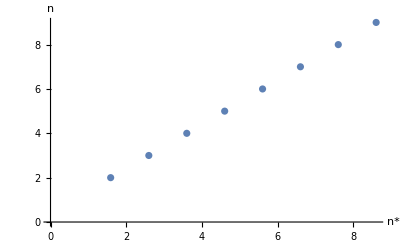

```mathematica
lp=ListPlot[points,AxesLabel->{"n*","n"},AxesOrigin->{0,0}]
```

```mathematica
Fit[points,{1,x},x]
```

0.408455+0.998787 x

```mathematica
model[x_,{m_,b_}]:=m x+b
aguess={.4,.4};
```

```mathematica
With[{aa={m,b}},nlm=NonlinearModelFit[points,model[x,aa],{aa,aguess}ᵀ,x]]
```

FittedModel[0.408455+0.998787 x]

```mathematica
a={m,b}/.nlm["BestFitParameters"]
```

{0.998787,0.408455}

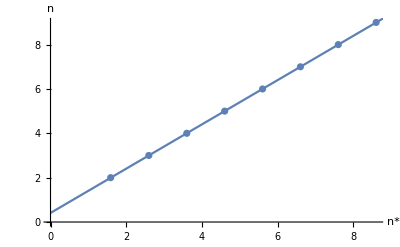

```mathematica
Show[lp,Plot[model[x,a],{x,0,9}]]
```

17) Now repeat, but with your calculated energy levels. Fit to find E_∞ and from that deduce your ionization potential and quantum defect and compare to experiment.

For #17, it is not possible to do the n* vs n plot as in 16, since you don’t know the ionization potential beforehand.  So you will need to fit to Eq 10. E_n-E_2=IP-1/(2(n-δ)^2). Also, you should compare your IP you get from the quantum defect analysis to the one you get from just comparing the results of #4 and #14

```mathematica
LHS=eval-eval⟦1⟧
```

{0.,0.121064,0.156001,0.170775,0.178382,0.182937,0.188092,0.200768}

```mathematica
model[n_,{IP_,δq_}]:=IP-1/(2(n-δq)^2)
aguess={.4,.4};
```

```mathematica
points=Table[{n⟦i⟧,LHS⟦i⟧},{i,1,8}]
```

{{2,0.},{3,0.121064},{4,0.156001},{5,0.170775},{6,0.178382},{7,0.182937},{8,0.188092},{9,0.200768}}

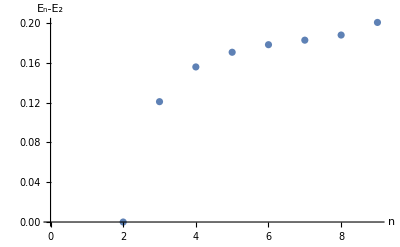

```mathematica
lp=ListPlot[points,AxesLabel->{"n","E_n-E_2"},AxesOrigin->{0,0}]
```

```mathematica
With[{aa={IP,δq}},nlm=NonlinearModelFit[points,model[x,aa],{aa,aguess}ᵀ,x]]
```

FittedModel[0.196945-1/(2 (-«20»+x)^2)]

```mathematica
a={IP,δq}/.nlm["BestFitParameters"]
```

{0.196945,0.409227}

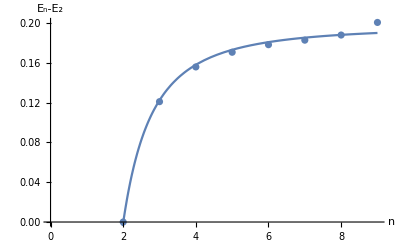

```mathematica
Show[lp,Plot[model[x,a],{x,0,9}]]
```